Example 1

```mathematica
eq=x^2+2*x-2==0
```

-2+2 x+x^2==0

```mathematica
Solve[eq,{x}]
```

{{x→-1-√3},{x→-1+√3}}

```mathematica
sol[[2]]
```

Part::partd: Part specification sol⟦2⟧ is longer than depth of object.

sol⟦2⟧

```mathematica
sol[[1,1,2]]
```

Part::partd: Part specification sol⟦1,1,2⟧ is longer than depth of object.

sol⟦1,1,2⟧

```mathematica
eq2=x^2+3*y^2-10==0
```

-10+x^2+3 y^2==0

```mathematica
ysol=Solve[eq2,y]
```

{{y→-(√(10-x^2))/(√3)},{y→(√(10-x^2))/(√3)}}

```mathematica
y1=ysol[[1,1,2]]
```

-(√(10-x^2))/(√3)

```mathematica
y2=ysol[[2,1,2]]
```

(√(10-x^2))/(√3)

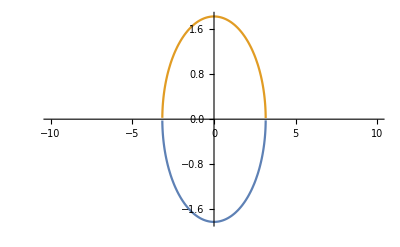

```mathematica
Plot[{y1,y2},{x,-10,10}]
```